```mathematica
<<MaTeX`
SetOptions[MaTeX,"Preamble"->{"\\usepackage{mathtext}" ,
"\\usepackage[T2A]{fontenc}",
"\\usepackage[utf8]{inputenc}",
"\\usepackage[english,russian]{babel}",
"\\usepackage{units}"}];
```

```mathematica
files=FileNames["*.csv",NotebookDirectory[]]
```

{/Users/yaroslav/Desktop/dataset.csv,/Users/yaroslav/Desktop/datasethi.csv,/Users/yaroslav/Desktop/hi.csv,/Users/yaroslav/Desktop/Untitled.csv}

```mathematica
importfile = files⟦1⟧
```

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
raw={{"a","n"},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}
```

{{a,n},{0,653},{10,609},{20,556},{30,525},{40,467},{50,413},{60,367},{70,331},{80,298},{90,268},{103,236}}

```mathematica
dataset=makeDataset[raw]
```

```mathematica
dataset1=dataset[All,<|"a"->(1/Around[#n,1]&),"b"->(1-Cos[ π Around[#a,1] /180]&)|>]
```

```mathematica
MantErr[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10,Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;2⟧],10]/10]
MantExp[a_]:=If[10≤Round[FromDigits[RealDigits[a["Uncertainty"]]⟦1,;;3⟧],10]/10≤19,MantissaExponent[a["Uncertainty"]]⟦2⟧-2,MantissaExponent[a["Uncertainty"]]⟦2⟧-1]
DigVal[a_]:=If[RealAbs[a["Value"]/10^MantExp[a]]<.01,MantissaExponent[MantErr[a]]⟦2⟧,MantissaExponent[a["Value"]]⟦2⟧-MantExp[a]+1]
MantVal[a_]:=If[RealAbs[a["Value"]/10^MantExp[a]]<.01,0,Sign[a["Value"]]Round[FromDigits[RealDigits[a["Value"]]⟦1,;;DigVal[a]⟧],10]/10]
hiTeXForm[x_]:=Which[Head[x]===Real||Head[x]===Integer,IntegerPart[x],-3≤MantExp[x]≤-1,ToString[Row[{PaddedForm[MantVal[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}],"(",MantErr[x],")"}]],MantExp[x]==0,ToString[Row[{MantVal[x],"(",MantErr[x],")"}]],True,ToString[Row[{MantVal[x],"(",MantErr[x],")e",MantExp[x]}]]]
hiTeXFormVal[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[x["Value"],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantVal[x]]
hiTeXFormErr[x_]:=Which[Head[x]===Real,IntegerPart[x],MantExp[x]≠0,ToString[PaddedForm[MantErr[x]*10.^MantExp[x],{DigVal[x],Abs[MantExp[x]]},NumberPadding->{"","0"}]],MantExp[x]==0,MantErr[x]]
```

```mathematica
dataset3=dataset1[All,<|"aexp"->(hiTeXForm[#a]&),"bexp"->(hiTeXForm[#b]&)|>]
```

```mathematica
dataset4=dataset1[All,<|"TexpAbs"->(hiTeXFormVal[#T]&),"TexpErr"->(hiTeXFormErr[#T]&),"WexpAbs"->(hiTeXFormVal[#W]&),"WexpErr"->(hiTeXFormErr[#W]&)|>]
```

```mathematica
Export[NotebookDirectory[]<>"datasethi.csv",dataset3,"TextDelimiters"->""]
```

/Users/yaroslav/Desktop/datasethi.csv

```mathematica
raw={Table[n+RandomInteger[],{n,10}],Table[n,{n,10}]}
```

{{2,2,3,4,6,7,7,8,9,11},{1,2,3,4,5,6,7,8,9,10}}

```mathematica
data=data3
fit=NonlinearModelFit[data,b-a/(1+((x-X)/(c/2))^2),{a,b,c,X},x](*   f = a + b * x   *)
fit["ParameterTable"];
a=Around[fit["BestFitParameters"]⟦1⟧,fit["ParameterErrors"]⟦1⟧]
b=Around[fit["BestFitParameters"]⟦2⟧,fit["ParameterErrors"]⟦2⟧]
(*fit["BestFitParameters"]⟦1⟧
fit["BestFitParameters"]⟦2⟧*)
(*hiTeXForm[a]
hiTeXForm[b]*)
Show[ListPlot[dataerr],Plot[fit["BestFitParameters"]⟦1⟧+fit["BestFitParameters"]⟦2⟧x,{x,Min[data⟦All,1⟧],Max[data⟦All,1⟧]}]]
```

FittedModel[-0.233216+0.971731 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.233216 | 0.385588 | -0.60483 | 0.56205
x | 0.971731 | 0.0585976 | 16.5831 | 1.76621×10^-7

-0.20.4

0.970.06

0.2(4)

0.97(6)

```mathematica
data=data3
fit=NonlinearModelFit[data,b-a/(1+((x-X)/(c/2))^2),{a,{b,29500},{c,1},X},x]//Normal
```

{{-6.35,29143.8},{-7.95,29176.5},{-7.52,29262.9},{-7.,29330.1},{-6.67,29183.5},{-6.08,29084.},{-5.65,29298.},{-5.26,29192.2},{-4.78,29141.6},{-4.37,29166.4},{-3.73,29260.7},{-3.24,29226.8},{-2.64,29228.4},{-1.88,29196.6},{-1.09,29203.2},{-0.32,29096.5},{4.93,29526.2},{6.24,29589.7},{5.89,29510.2},{5.48,29599.2},{5.2,29523.8},{4.7,29405.4},{4.42,29320.7},{4.06,29127.8},{3.72,29009.},{3.4,28819.2},{2.87,27559.4},{2.52,26662.3},{2.09,27344.1},{1.47,29095.},{0.9,29360.4},{0.29,29334.6}}

29345.2-2893.02/(1+4.73178 (-2.4442+x)^2)

```mathematica
fit=.
```

```mathematica
data=.
```

```mathematica
data1=;
data2=Table[0.5n,{n,19}];
data[1]={data2,data1ᵀ//Flatten}ᵀ;
data[2]=;
data[3]=;
data[4]=;
data[5]=;
fit[2]=NonlinearModelFit[data[2],{b-a/(1+((x-X)/(c/2))^2),c≥0},{a,{b,29500},{c,1},X},x];
fit[3]=NonlinearModelFit[data[3],{b-a/(1+((x-X)/(c/2))^2),c≥0},{a,{b,13000},{c,1},X},x];
fit[4]=NonlinearModelFit[data[4],{b-a/(1+((x-X)/(c/2))^2),c≥0},{a,{b,3200},{c,1},X},x];
fit[5]=NonlinearModelFit[data[5],{b-a/(1+((x-X)/(c/2))^2),c≥0},{a,{b,32000},{c,1},{X,0.3}},x];
(*Table[dataset[i]=makeDataset[{{"v","I"}}~Join~data[i]],{i,5}];
Table[datasetWE[i]=dataset[i][All,<|"v"->(#v&),"I"->(Around[#I,(#I)/(√20)]&)|>],
{i,5}];*)
```

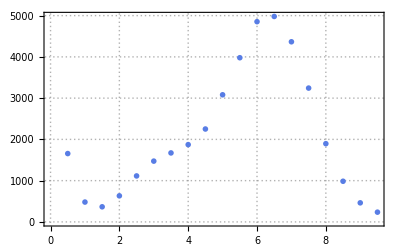

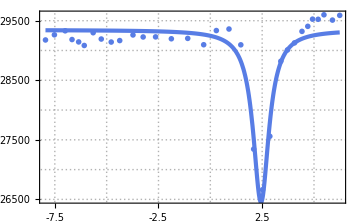
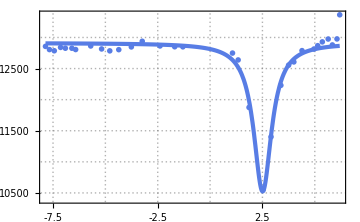
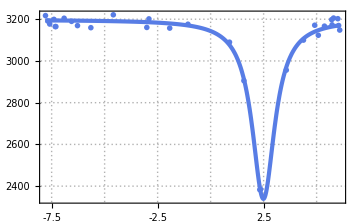
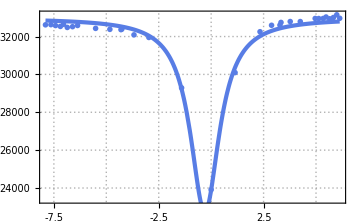

```mathematica
ListPlot[data[1],Frame->True,PlotTheme->"Business",FrameStyle->Black,GridLines->Automatic,LabelStyle->{NumberPoint->","},BaseStyle->{FontFamily->"Comic Sans MS"},(*PlotLegends->MaTeX@functions,*)FrameLabel->MaTeX@{"E,\\text{ эВ}","I,\\nicefrac{1}{\\text{с}}"}]
Table[Show[ListPlot[data[i],PlotTheme->"Business",Frame->True,FrameStyle->Black,GridLines->Automatic,LabelStyle->{NumberPoint->","},BaseStyle->{FontFamily->FontFamily->"Comic Sans MS"},(*PlotLegends->MaTeX@functions,*)FrameLabel->MaTeX@{"v,\\nicefrac{\\text{мм}}{\\text{с}}","I,\\nicefrac{1}{\\text{с}}"},ImageSize->Medium,PlotRange->All],
Plot[fit[i]//Normal,{x,Min[data[i]⟦All,1⟧],Max[data[i]⟦All,1⟧]},PlotRange->All,PlotTheme->"Business"]],{i,2,5}]
```

```mathematica
datasetf=makeDataset[{{"n","a","b","c","X","y"}}~Join~Table[{i-1}~Join~MapThread[Around,{{a,b,c,X}/.fit[i]["BestFitParameters"],fit[i]["ParameterErrors"]}]~Join~{Normal[fit[i]]},{i,2,5}]]
datasetftf=datasetf[All,<|"nexp"->(#n&),"aexp"->(hiTeXForm[#a]&),"bexp"->(hiTeXForm[#b]&),"cexp"->(hiTeXForm[#c]&),"Xexp"->(hiTeXForm[#X]&)|>]
Export[NotebookDirectory[]<>"dataset.csv",datasetftf,"TextDelimiters"->""]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/6.1/dataset.csv

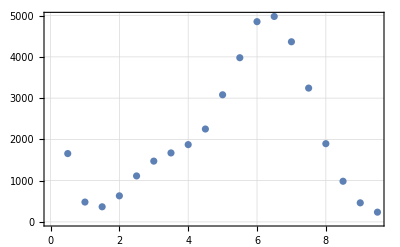

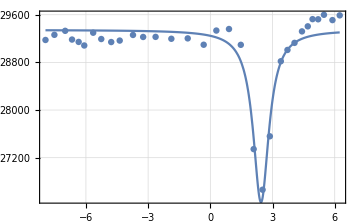
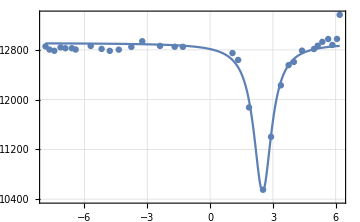
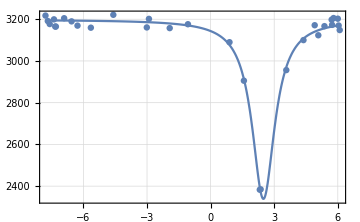
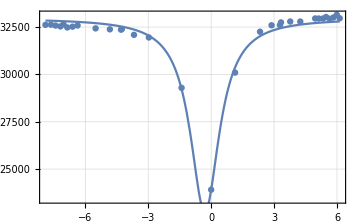

```mathematica
ListPlot[data[1],Frame->True,FrameStyle->Black,GridLines->Automatic,LabelStyle->{NumberPoint->","},BaseStyle->{FontFamily->"CMU Serif"},(*PlotLegends->MaTeX@functions,*)FrameLabel->MaTeX@{"E,\\text{ эВ}","I,\\nicefrac{1}{\\text{с}}"}]
Table[Show[ListPlot[data[i],Frame->True,FrameStyle->Black,GridLines->Automatic,LabelStyle->{NumberPoint->","},BaseStyle->{FontFamily->"CMU Serif"},(*PlotLegends->MaTeX@functions,*)FrameLabel->MaTeX@{"v,\\nicefrac{\\text{мм}}{\\text{с}}","I,\\nicefrac{1}{\\text{с}}"},ImageSize->Medium,PlotRange->All],
Plot[fit[i]//Normal,{x,Min[data[i]⟦All,1⟧],Max[data[i]⟦All,1⟧]},PlotRange->All]],{i,2,5}]
```

```mathematica
MapThread[Around,{fit[2]["BestFitParameters"],fit[2]["ParameterErrors"]}]
```

{a→2893.02201.,b→29345.240.,c→-0.9194280.10,X→2.44420.034}

```mathematica
{a,b,c,X}/.fit[2]["BestFitParameters"]
```

{2893.02,29345.2,-0.919428,2.4442}

```mathematica
Ν=13.8
```

13.8

```mathematica
ε=(b-y(X))/(b-Ν)
(2#c)/(3*10^11)23.8
(#X)/(3*10^11)*23.8 10^3
```

```mathematica
datasetf2=datasetf[All,<|"n"->(#n&),"eps"->(10^2(#b-#y)/(#b-Ν)/.{x->#X}&),"eps"->(10^2(#b-#y)/(#b-Ν)/.{x->#X}&),"gamma"->(2#c&),"gamma2"->((2#c)/(3*10^11)23.8 10^3*10^7&),"vp"->(#X&),"dE"->((#X)/(3*10^11)*23.8 10^3 * 10^7&)|>]
datasetftf=datasetf2[All,<|"nexp"->(#n&),"epsexp"->(hiTeXForm[#eps]&),"gexp"->(hiTeXForm[#gamma]&),"gexpt"->(hiTeXForm[#gamma2]&),"vp"->(hiTeXForm[#vp]&),"dE"->(hiTeXForm[#dE]&)|>]
Export[NotebookDirectory[]<>"dataset2.csv",datasetftf,"TextDelimiters"->""]
```

/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/6.1/dataset2.csv

```mathematica
Table[MapThread[Around,{{a,b,c,X}/.fit[i]["BestFitParameters"],fit[i]["ParameterErrors"]}],{i,2,5}]
```

FittedModel::constr: The property values {ParameterErrors} assume an unconstrained model. The results for these properties may not be valid, particularly if the fitted parameters are near a constraint boundary.

General::stop: Further output of FittedModel::constr will be suppressed during this calculation.

{{2893.201.,29345.40.,0.920.10,2.4440.034},{2387.125.,12911.27.,1.030.08,2.510.04},{859.33.,3198.5.,1.300.07,2.490.04},{10231.544.,32967.62.,1.680.12,-0.300.05}}

```mathematica
Normal[fit[2]]
```

29345.2-2893.02/(1+4.73178 (-2.4442+x)^2)

```mathematica
dataset1=makeDataset[{{"I","E"}}~Join~data[1]];
dataset1f=dataset1[All,<|"Ione"->(#I&),"Eone"->(hiTeXForm[#E]&)|>];
Export[NotebookDirectory[]<>"dataset1f.csv",dataset1f,"TextDelimiters"->""]
```

/Users/yaroslav/mipt/bachelor-3/semester-2/laboratory/6.1/dataset1f.csv

```mathematica
Table[datasetraw[i]=makeDataset[{{"I","v"}}~Join~data[i]],{i,2,5}];
Table[datasetrawf[i]=datasetraw[i][All,<|StringForm["I``",i]->(hiTeXForm[#I]&),StringForm["v``",i]->(hiTeXForm[#v]&)|>],{i,2,5}]
(*Export[NotebookDirectory[]<>"dataset1f.csv",dataset1f,"TextDelimiters"->""]*)
```

{,,,}

```mathematica
datasetrawf[2]=datasetraw[2][All,<|"Itwo"->(#I&),"vtwo"->(#v&)|>];
Export[NotebookDirectory[]<>"dataset2f.csv",datasetrawf[2],"TextDelimiters"->""];
datasetrawf[3]=datasetraw[3][All,<|"Ithree"->(#I&),"vthree"->(#v&)|>];
Export[NotebookDirectory[]<>"dataset3f.csv",datasetrawf[3],"TextDelimiters"->""];
datasetrawf[4]=datasetraw[4][All,<|"Ifour"->(#I&),"vfour"->(#v&)|>];
Export[NotebookDirectory[]<>"dataset4f.csv",datasetrawf[4],"TextDelimiters"->""];
datasetrawf[5]=datasetraw[5][All,<|"Ifive"->(#I&),"vfive"->(#v&)|>];
Export[NotebookDirectory[]<>"dataset5f.csv",datasetrawf[5],"TextDelimiters"->""];
```

ClearAll::ssym: datasetrawf[_] is not a symbol or a string.

```mathematica
Grid[({{1, 1, 1}, {1, 1, 1}, {1, 1, 1}}),Frame->All]//TeXForm
```

\begin{array}{ccc}
 1 & 1 & 1 \\
 1 & 1 & 1 \\
 1 & 1 & 1 \\
\end{array}

```mathematica
datasetf2//Normal
```

{<|n→1,eps→9.860.14,gamma→1.840.21,gamma2→1.460.16,vp→2.4440.034,dE→1.9390.027|>,<|n→2,eps→18.510.21,gamma→2.070.16,gamma2→1.640.13,vp→2.510.04,dE→1.9900.029|>,<|n→3,eps→26.970.17,gamma→2.590.13,gamma2→2.060.10,vp→2.490.04,dE→1.9760.034|>,<|n→4,eps→31.050.20,gamma→3.370.24,gamma2→2.670.19,vp→-0.300.05,dE→-0.240.04|>}

```mathematica
Around[3,1]//TeXForm
```

3.0\pm 1.0